# Lorenz system

Bohan Lu

The Lorenz system is a well-known model that exhibits chaotic behavior. It is a coupled first order linear dynamical system described by:

```mathematica
x'[t] == σ*(y[t]-x[t])
y'[t] == x[t]*(ρ-z[t])-y[t]
z'[t] == x[t]*y[t]-β*z[t]
```

This model has numerous applications, and the most widely recognized of which is weather forecasting. In order to visualize the behavior of this system, we need to solve the above system of differential equations with different parameter values σ, ρ, and β.

```mathematica
Lorenz[σ_,ρ_,β_,x0_,y0_,z0_,tmax_]:= NDSolve[{x'[t] == σ*(y[t]-x[t]) ,y'[t] == x[t]*(ρ-z[t])-y[t],z'[t] == x[t]*y[t]-β*z[t],x[0]==x0, y[0]==y0, z[0]==z0},{x,y,z},{t,tmax}];
```

To start off, we initialize the parameters to be σ = ρ = β = 1, the initial values to be x[0] = y[0] = z[0] = 1, and solve it using NDSolve running from t = 0 to t = 100.

```mathematica
s1 = Lorenz[1, 1, 1, 1, 1, 1, 100];
```

To visualize it, we use parametric plot:

```mathematica
ParametricPlot3D[Evaluate[{x[t], y[t], z[t]} /. s1], {t, 0, 100},AxesLabel->{x,y,z}]
```

-Graphics3D-

It seems like nothing quite interesting is going on, so we would like to change our parameter values to ones that reflect a real world system, for example, the atmospheric convection. The suggested values for this system are :

```mathematica
s2 = Lorenz[10, 28, 8/3, 5, 5, 5, 100];
```

```mathematica
ParametricPlot3D[Evaluate[{x[t], y[t], z[t]} /. s2], {t, 0, 20},AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
Animate[Module[{sol=Lorenz[10, 28, 8/3, 5, 5, 5, T]},ParametricPlot3D[Evaluate[{x[t], y[t], z[t]} /. s2], {t, 0, T},PerformanceGoal->"Quality",ImageSize->400]],{T,0.001,20},AnimationRate->.5,AnimationDirection->Forward,AnimationRunning->False]
```

We observe two attractors showing up, and the curve orbits around one of the attractors at time before moving off to orbit around the other attractor. To have a better understanding of the behavior, we project the plot to three 2D versions:

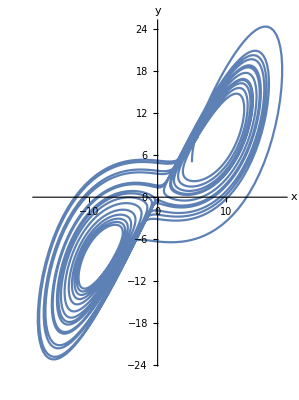

```mathematica
ParametricPlot[Evaluate[{x[t], y[t]} /. s2], {t, 0, 20},AxesLabel->{x,y}]
```

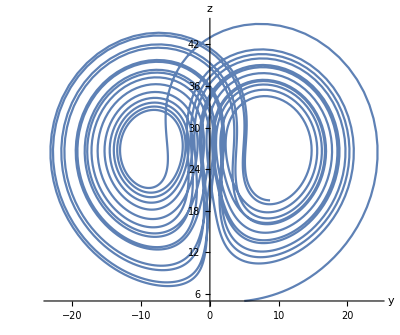

```mathematica
ParametricPlot[Evaluate[{y[t], z[t]} /. s2], {t, 0, 20},AxesLabel->{y,z}]
```

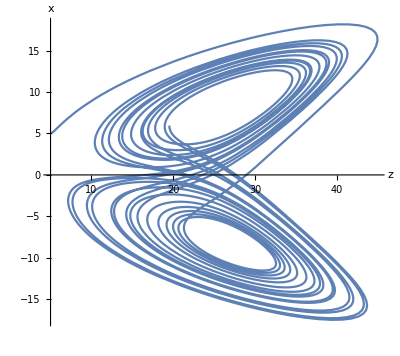

```mathematica
ParametricPlot[Evaluate[{z[t], x[t]} /. s2], {t, 0, 20},AxesLabel->{z,x}]
```

Comparing the projections with the 3D plot, we see that the parts that overlap in the projections do not actually cross each other. To further understand the behavior, we can also plot the time series.

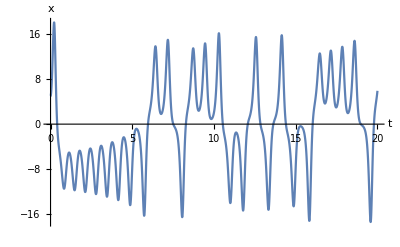

```mathematica
Plot[Evaluate[x[t] /. s2],{t, 0, 20},AxesLabel->{t,x}]
```

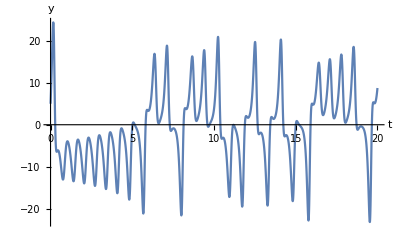

```mathematica
Plot[Evaluate[y[t] /. s2],{t, 0, 20},AxesLabel->{t,y}]
```

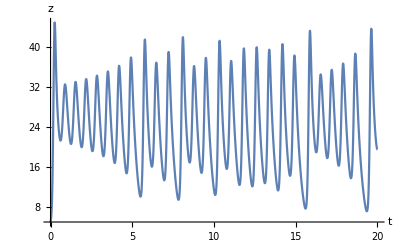

```mathematica
Plot[Evaluate[z[t] /. s2],{t, 0, 20},AxesLabel->{t,z}]
```

Looking at the time series for x and y, we sense a existence of chaotic behavior. To verify that we are indeed in the chaotic regime of the parameter space, we apply a slight perturbation to the initial conditions, and observe how sensitive the time evolution depends on that perturbation. Let the perturbation be, for instance, 10^-6. The perturbed value is thus

```mathematica
p = 5+1*^-6;
```

```mathematica
s3 = Lorenz[10, 28, 8/3, p, p, p, 200];
```

```mathematica
s4 = Lorenz[10, 28, 8/3, 5, 5, 5, 200];
```

```mathematica
ParametricPlot3D[{Evaluate[{x[t], y[t], z[t]} /. s3],Evaluate[{x[t], y[t], z[t]} /. s4]}, {t, 0, 200},AxesLabel->{x,y,z},PlotStyle->Automatic,PlotLegends->{"s3","s4"}]
```

-Graphics3D-

Clearly, the plot with the original initial conditions diverge from the one with added perturbation in the long run (from t = 0 to t = 200). This sensitive dependence on initial conditions confirms that the parameter values {σ,ρ,β}={10,28,8/3} indeed lie in the chaotic regime.